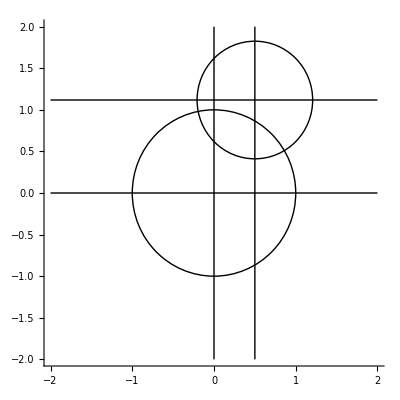

```mathematica
Graphics[{Circle[{0,0},1], Circle[{1/2,√5/2},1/√2],Thick,Line[{{-2,0},{2,0}}],Thick,Line[{{0,-2},{0,2}}],Line[{{1/2,-2},{1/2,2}}],Line[{{-2,√5/2},{2,√5/2}}]}, Axes->True]
```

```mathematica
MatrixForm[{{0,0,-1,0},{1,0,1,0},{0,0,0,-1},{√5,0,0,1},{-1,1,0,0},{Sqrt[2],Sqrt[2],Sqrt[2]/2,Sqrt[5/2]}}]
```

(0 | 0 | -1 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | -1
√5 | 0 | 0 | 1
-1 | 1 | 0 | 0
√2 | √2 | 1/(√2) | √(5/2))

Create some function that takes inverse coordinates, checks for each if the 2nd coordinate is 0 --> line, measures greatest horizontal and vertical distance and goes .5 past that. If not line, draws circle.